```mathematica
practicle 1
```

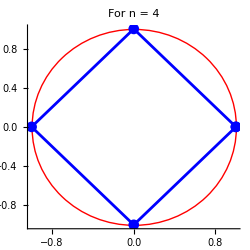

```mathematica
n=4;
Points=Table[{Re[Exp[2*Pi*I*k/n]],Im[Exp[2*Pi*I*k/n]]},{k,0,n-1}];
Points=Append[Points,Points[[1]]];
A1= Show[Graphics[{Thick,Red,Circle[{0,0},1]}],ListLinePlot[{Points},PlotStyle->Blue,PlotMarkers->Automatic],Axes->True,ImageSize->250,PlotLabel-> "For n = 4"]
```

```mathematica
ClearAll;
```

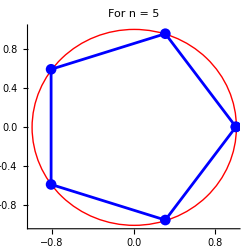

```mathematica
n=5;
Points=Table[{Re[Exp[2*Pi*I*k/n]],Im[Exp[2*Pi*I*k/n]]},{k,0,n-1}];
Points=Append[Points,Points[[1]]];
A1= Show[Graphics[{Thick,Red,Circle[{0,0},1]}],ListLinePlot[{Points},PlotStyle->Blue,PlotMarkers->Automatic],Axes->True,ImageSize->250,PlotLabel-> "For n = 5"]
```

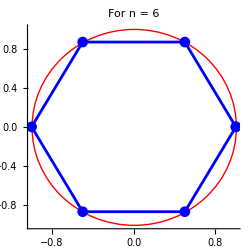

```mathematica
n=6;
Points=Table[{Re[Exp[2*Pi*I*k/n]],Im[Exp[2*Pi*I*k/n]]},{k,0,n-1}];
Points=Append[Points,Points[[1]]];
A1= Show[Graphics[{Thick,Red,Circle[{0,0},1]}],ListLinePlot[{Points},PlotStyle->Blue,PlotMarkers->Automatic],Axes->True,ImageSize->250,PlotLabel-> "For n = 6"]
```

# Practicle 2

```mathematica
ClearAll;
```

```mathematica
Points = ComplexExpand[z /. Solve[z^3-8*I == 0]] 
Realpart=Re[Points];
Imaginarypart=Im[Points];
Data=Transpose[{Realpart,Imaginarypart}];
Data= Append[Data,Data[[1]]];
ListPlot[Map[Labeled[#,#]&, Data],PlotStyle->{PointSize[0.03]},PlotRange->{-3,2},ImageSize->300]
Show[Graphics[{Thick,Red,Circle[{0,0},2]}],ListLinePlot[Map[Labeled[#,#]&,Data],PlotStyle->Blue,PlotMarkers->Automatic],Axes->True,ImageSize->250]
```

{-2 ⅈ,ⅈ+√3,ⅈ-√3}

-Graphics-

-Graphics-

```mathematica
ClearAll;
```

```mathematica
A1 = ParametricPlot[{4*Cos[t], 2*Sin[t]},
{t, 0, 2*Pi}, Frame ->True , ImageSize -> 300, PlotLabel -> "Ellipse"]
```

-Graphics-

```mathematica
A2 = ParametricPlot[{4*Cos[t]*Cos[Pi/6]-2*Sin[t]*Sin[Pi/6],4*Cos[t]*Sin[Pi/6]+2*Sin[t]*Cos[Pi/6]},{t,0,2*Pi},Frame->True,ImageSize->300,PlotLabel->"Ellipse"]
```

-Graphics-

-Graphics-